```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Projects\research\Diffusion-Lattice-Distribution-Set-Theory

```mathematica
Get["./base_package/SOHR_base.m"]
```

```mathematica
Names[$Context<>"*"]
```

{CalculateLimit,ExponentialBasis,ExponentialBasis$,GetExponentialBase,GetHMatrix,GetPathwayProbabilityVector,Hij,HMatrix,HMatrix$,i,j,l,m,n,output,output$,P,q,t,ToSubScriptExpression}

# A⇌_k_1^k_1B type reaction network

```mathematica
HMatrix = GetHMatrix[5,5];
ExponentialBasis = GetExponentialBase[5];
HMatrix//MatrixForm
ExponentialBasis//MatrixForm
```

(1 | 0 | 0 | 0 | 0
k1/(-k1+k2) | k1/(k1-k2) | 0 | 0 | 0
(k1 k2)/((-k1+k2) (-k1+k3)) | (k1 k2)/((k1-k2) (-k2+k3)) | (k1 k2)/((k1-k3) (k2-k3)) | 0 | 0
(k1 k2 k3)/((-k1+k2) (-k1+k3) (-k1+k4)) | (k1 k2 k3)/((k1-k2) (-k2+k3) (-k2+k4)) | (k1 k2 k3)/((k1-k3) (k2-k3) (-k3+k4)) | (k1 k2 k3)/((k1-k4) (k2-k4) (k3-k4)) | 0
(k1 k2 k3 k4)/((-k1+k2) (-k1+k3) (-k1+k4) (-k1+k5)) | (k1 k2 k3 k4)/((k1-k2) (-k2+k3) (-k2+k4) (-k2+k5)) | (k1 k2 k3 k4)/((k1-k3) (k2-k3) (-k3+k4) (-k3+k5)) | (k1 k2 k3 k4)/((k1-k4) (k2-k4) (k3-k4) (-k4+k5)) | (k1 k2 k3 k4)/((k1-k5) (k2-k5) (k3-k5) (k4-k5)))

(ⅇ^(-k1 t)
ⅇ^(-k2 t)
ⅇ^(-k3 t)
ⅇ^(-k4 t)
ⅇ^(-k5 t))

```mathematica
PathProbV = HMatrix.ExponentialBasis;
```

```mathematica
PathProbV/.{k5->Subscript[k, 5],k4->Subscript[k, 4],k3->Subscript[k, 3],k2->Subscript[k, 2],k1->Subscript[k, 1]}//MatrixForm
```

(ⅇ^(-t k_1)
(ⅇ^(-t k_2) k_1)/(k_1-k_2)+(ⅇ^(-t k_1) k_1)/(-k_1+k_2)
(ⅇ^(-t k_3) k_1 k_2)/((k_1-k_3) (k_2-k_3))+(ⅇ^(-t k_1) k_1 k_2)/((-k_1+k_2) (-k_1+k_3))+(ⅇ^(-t k_2) k_1 k_2)/((k_1-k_2) (-k_2+k_3))
(ⅇ^(-t k_4) k_1 k_2 k_3)/((k_1-k_4) (k_2-k_4) (k_3-k_4))+(ⅇ^(-t k_1) k_1 k_2 k_3)/((-k_1+k_2) (-k_1+k_3) (-k_1+k_4))+(ⅇ^(-t k_2) k_1 k_2 k_3)/((k_1-k_2) (-k_2+k_3) (-k_2+k_4))+(ⅇ^(-t k_3) k_1 k_2 k_3)/((k_1-k_3) (k_2-k_3) (-k_3+k_4))
(ⅇ^(-t k_5) k_1 k_2 k_3 k_4)/((k_1-k_5) (k_2-k_5) (k_3-k_5) (k_4-k_5))+(ⅇ^(-t k_1) k_1 k_2 k_3 k_4)/((-k_1+k_2) (-k_1+k_3) (-k_1+k_4) (-k_1+k_5))+(ⅇ^(-t k_2) k_1 k_2 k_3 k_4)/((k_1-k_2) (-k_2+k_3) (-k_2+k_4) (-k_2+k_5))+(ⅇ^(-t k_3) k_1 k_2 k_3 k_4)/((k_1-k_3) (k_2-k_3) (-k_3+k_4) (-k_3+k_5))+(ⅇ^(-t k_4) k_1 k_2 k_3 k_4)/((k_1-k_4) (k_2-k_4) (k_3-k_4) (-k_4+k_5)))

```mathematica
PPV = PathProbV;
For[i=Length[PPV],i≥1,i--,
For[j=i-1,j≥1,j--,PPV⟦i⟧=CalculateLimit[PPV⟦i⟧,j+1,j]]
];
```

```mathematica
PPV/.{k1->Subscript[k, 1]}//MatrixForm
```

(ⅇ^(-t k_1)
ⅇ^(-t k_1) t k_1
1/2 ⅇ^(-t k_1) t^2 k_1^2
1/6 ⅇ^(-t k_1) t^3 k_1^3
1/24 ⅇ^(-t k_1) t^4 k_1^4)

## Has pattern of 1/(n!)ⅇ^(-k_1 t) k_1^n t^n, this is exactly the Poisson distribution Pr(N_t=n) =f(n; λt) =e^-λt/(n!)(λt)^n

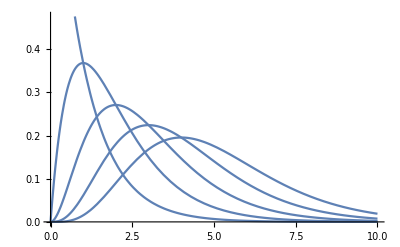

```mathematica
Plot[PPV/.k1->1.0,{t,0,10}]
```

```mathematica
(*Names[$Context<>"*"]*)
```

## Think of set {0,1,2,3,...} represent path length Pathway probability has form of p_n=c_n e^-k_nt, in continuous x-axis, the distribution function is P(x)=∑_nϵℕ P_n δ(x-n) The definition of characteristic function states that G(z)=⟨e^izX⟩=∫_I e^izx P(x)dx G(z)=∑_nϵℕ P_n e^izn G(z)=∑_nϵℕ c_n e^-k_nt e^izn